```mathematica
μ1=3.986004356*^14 (*m^3/s^2*);
μ2=4.90280014595616*^12 (*m^3/s^2*);
r3=6371*10^3 (*m*);
RM=385000000 (*m*);
h1 = 200000 (*m - высота опорной орбиты*);
Ra = 150000000 (*высота целевой орбиты*);
m1 = 20000 (*kg*);
mKVTKemp = 24000-19600 (*kg*);
```

## Параметры опорной круговой НОО

```mathematica
e1=0;
p1=(r3+h1)*(1+e1);
v1=√(μ1/p1)
```

7788.49

# Гомановский перелёт

## Параметры переходной орбиты

```mathematica
e2=(Ra-(r3+h1))/(Ra+(r3+h1))//N
p2=(r3+h1)*(1+e2)//N
v2p=√(μ1/p2)*(1+e2)
v2a=√(μ1/p2)*(1-e2)
Δv1=v2p-v1
```

0.916064

1.25905×10^7

10781.

472.279

2992.49

```mathematica
1971300000000/156571
```

10781.

472.279

2992.49

## Параметры целевой круговой орбиты радиусом Ra

```mathematica
e3=0;
p3=Ra;
v3=√(μ1/p3)
Δv2=v3-v2a
```

1630.13

1157.86

```mathematica
(*Суммарная затрата характеристической скорости*)
Δv=Abs[Δv1]+Abs[Δv2]
```

4150.34

```mathematica
Δv
```

4150.34

```mathematica
RaList=Table[36*step*10^6,{step, 1.5,15,0.5}]
```

{5.4×10^7,7.2×10^7,9.×10^7,1.08×10^8,1.26×10^8,1.44×10^8,1.62×10^8,1.8×10^8,1.98×10^8,2.16×10^8,2.34×10^8,2.52×10^8,2.7×10^8,2.88×10^8,3.06×10^8,3.24×10^8,3.42×10^8,3.6×10^8,3.78×10^8,3.96×10^8,4.14×10^8,4.32×10^8,4.5×10^8,4.68×10^8,4.86×10^8,5.04×10^8,5.22×10^8,5.4×10^8}

```mathematica
T3=2π*√(Ra^3/μ1);
```

```mathematica
Clear[Tab1]
```

```mathematica
Tab1={{"N","Ra, тыс. км","Δv, км/c","Период обращения T, дней"}}
```

{{N,Ra, тыс. км,Δv, км/c,Период обращения T, дней}}

```mathematica
RaList[[1]]
```

5.4×10^7

```mathematica
For[i=1, i<=Length[RaList], i++,
AppendTo[Tab1, {i, RaList[[i]]/10^6, Δv/10^3 /.Ra->RaList[[i]],T3/3600/24 /.Ra->RaList[[i]]}]
]
Grid[Tab1, Frame -> All]
```

N | Ra, тыс. км | Δv, км/c | Период обращения T, дней
1 | 54. | 4.06286 | 1.4454
2 | 72. | 4.14607 | 2.22534
3 | 90. | 4.17291 | 3.11
4 | 108. | 4.17605 | 4.08821
5 | 126. | 4.16827 | 5.15173
6 | 144. | 4.1553 | 6.29421
7 | 162. | 4.13991 | 7.51052
8 | 180. | 4.12355 | 8.79642
9 | 198. | 4.10698 | 10.1483
10 | 216. | 4.09064 | 11.5632
11 | 234. | 4.07473 | 13.0383
12 | 252. | 4.05938 | 14.5713
13 | 270. | 4.04464 | 16.1601
14 | 288. | 4.03051 | 17.8027
15 | 306. | 4.017 | 19.4975
16 | 324. | 4.00409 | 21.2429
17 | 342. | 3.99174 | 23.0376
18 | 360. | 3.97994 | 24.88
19 | 378. | 3.96865 | 26.7692
20 | 396. | 3.95784 | 28.7038
21 | 414. | 3.94749 | 30.683
22 | 432. | 3.93756 | 32.7057
23 | 450. | 3.92803 | 34.7709
24 | 468. | 3.91888 | 36.8779
25 | 486. | 3.91009 | 39.0258
26 | 504. | 3.90162 | 41.2138
27 | 522. | 3.89347 | 43.4413
28 | 540. | 3.88562 | 45.7075

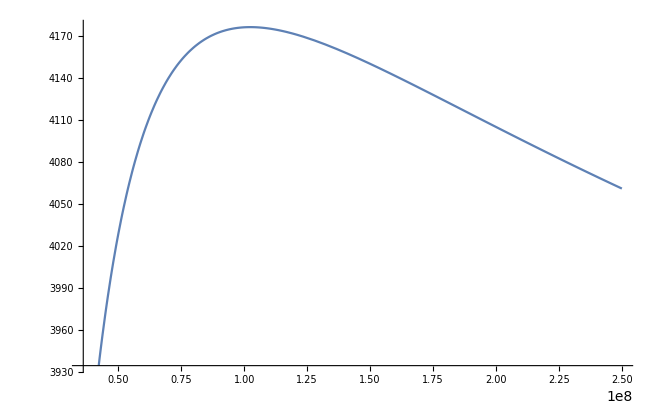

```mathematica
Plot[Δv,{Ra,36000000,250000000}]
```

# Биэллиптический перелёт (трёхимпульсный)

```mathematica
RaB=.
```

```mathematica
(*Перелёт на 1-ый эллипс*)
```

```mathematica
e2B=(RaB-(r3+h1))/(RaB+(r3+h1))//N
p2B=(r3+h1)*(1+e2B)//N
v2pB=√(μ1/p2B)*(1+e2B)
v2aB=√(μ1/p2B)*(1-e2B)
Δv1B=v2pB-v1
```

0.959132

1.28735×10^7

10901.5

227.408

3112.98

```mathematica
(*Перелёт на 2-ой эллипс*)
```

```mathematica
e3B=(RaB-Ra)/(RaB+Ra)//N
p3B=Ra*(1+e3B)//N
v3pB=√(μ1/p3B)*(1+e3B)//N
v3aB=√(μ1/p3B)*(1-e3B)//N
Δv2B=v3aB-v2aB//N
(*Перелёт на целевую орбиту*)
Δv3B=v3-v3pB//N
(*Суммарные затраты хар-ой скорости*)
ΔvB=Abs[Δv1B]+Abs[Δv2B]+Abs[Δv3B]//N
```

0.354839

2.03226×10^8

1897.44

903.541

676.133

-267.302

4056.41

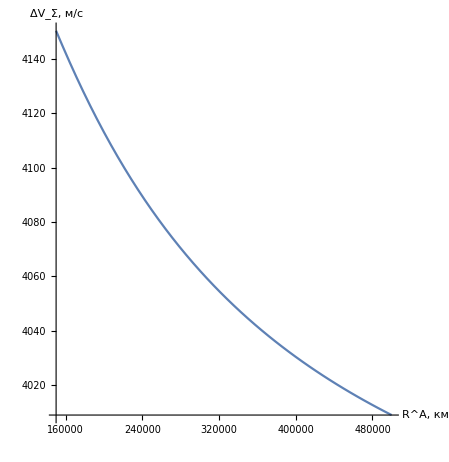

```mathematica
Plot[ΔvB/.RaB->x*1000,{x,150000,500000},AxesLabel->{"R^A, км", "ΔV_Σ, м/c"},PlotRange->All,LabelStyle->Directive[Black,Bold,Medium], AspectRatio->1.03]
```

```mathematica
Plot[ΔvB/.RaB->x 1000,{x,150000,600000},PlotTheme->"Detailed",AxesLabel->{"\!\(\*SuperscriptBox[\(R\), \(A\)]\), км","\!\(\*SubscriptBox[\(ΔV\), \(Σ\)]\), м/c"},PlotRange->All,LabelStyle->Directive[Black,Bold]]
```

```mathematica
FindMinimum[ΔvB,{RaB,3*10^8}]
```

{3827.67,{RaB→3.41697×10^8}}

```mathematica
Δv/.Ra->150000000
```

4150.34

```mathematica
Δv/.Ra->380000000
```

3967.42

# Переход на орбиту захоронения

```mathematica
Параметры орбиты захоронения
ezakh=(Ra-(r3+100000))/(Ra+(r3+100000));
pzakh=(r3+100000)*(1+ezakh);
vpzakh=√(μ1/pzakh)*(1+ezakh);
vazakh=√(μ1/pzakh)*(1-ezakh);
Δv1zakh=Abs[v3-vazakh];
Δv1zakh /.Ra-> 150000000
```

орбиты Параметры захоронения

1161.31

```mathematica
Vzakh=√((2μ1)/Ra);
Δv2zakh=Abs[v3-Vzakh];
Δv2zakh /.Ra-> 150000000
```

675.224

```mathematica
(*Выбираем отлёт в межпланетное пространство*)
```

```mathematica
mfzakh=Solve[(Δv2zakh/.Ra->150000000)==4500*Log[(mKVTKemp+mfzakh)/mKVTKemp],mfzakh][[1,1,2]]
```

712.325

# Затраты топлива при биэллиптическом перелёте, РБ КВТК (не подходит, если только КВТК2Б-А7В)

```mathematica
RaB=315000000
```

315000000

```mathematica
mf1=Solve[Δv3B==4500*Log[(m1+mKVTKemp+mfzakh+mf1)/(m1+mKVTKemp+mfzakh)],mf1][[1,1,2]]
```

2072.32

```mathematica
mf2=Solve[Δv2B==4500*Log[(m1+mKVTKemp+mfzakh+mf1+mf2)/(m1+mKVTKemp+mfzakh+mf1)],mf2][[1,1,2]]
```

2193.26

```mathematica
mf3=Solve[Δv1B==4500*Log[(m1+mKVTKemp+mfzakh+mf1+mf2+mf3)/(m1+mKVTKemp+mfzakh+mf1+mf2)],mf3][[1,1,2]]
```

29411.

```mathematica
mfuel=mfzakh+mf1+mf2+mf3
```

34388.9

# Перелёт на ТЭМ (Зевс), двигатель ИД-500

```mathematica
Jid500=70000 (*м/c*);
Fid500=0.75(*Н*);
Δmid500=Fid500/Jid500(*кг/c*);
nid500=16 (*кол-во двигателей*);
mzevs=20290(*kg*);
Δm=Δmid500*nid500;
F=Fid500*nid500;
```

## Сначала перелёт на КВТК на орбиту базирования, как можно выше

```mathematica
e2bo=(Rbo-(r3+h1))/(Rbo+(r3+h1))//N
p2bo=(r3+h1)*(1+e2bo)//N
v2pbo=√(μ1/p2bo)*(1+e2bo)
v2abo=√(μ1/p2bo)*(1-e2bo)
Δv1bo=v2pbo-v1
```

0.355532

8.9072×10^6

9067.93

4311.22

1279.44

```mathematica
e3bo=0;
p3bo=Rbo;
v3bo=√(μ1/p3bo)
Δv2bo=v3bo-v2abo
```

5370.31

1059.09

```mathematica
ezakhbo=(Rbo-(r3+70000))/(Rbo+(r3+70000))//N
pzakhbo=(r3+70000)*(1+ezakhbo)//N
vazakhbo=√(μ1/pzakhbo)*(1-ezakhbo)
Δv1zakhbo=Abs[v3bo-vazakhbo]
```

0.364229

8.787×10^6

4282.03

1088.28

```mathematica
Clear[mfzakhbo]
```

```mathematica
mfzakhbo=Solve[Δv1zakhbo==4500*Log[(mKVTKemp+mfzakhbo)/mKVTKemp],mfzakhbo][[1,1,2]];
```

```mathematica
mfzakhbo/.Rbo->(r3+hbo)
```

1203.8

```mathematica
Clear[mf1bo]
```

```mathematica
mf1bo=Solve[Δv2bo==4500*Log[(m1+mKVTKemp+mfzakhbo+mf1bo)/(m1+mKVTKemp+mfzakhbo)],mf1bo][[1,1,2]];
```

```mathematica
mf1bo/.Rbo->(r3+hbo)
```

6794.11

```mathematica
Clear[mf2bo]
```

```mathematica
mf2bo=Solve[Δv1bo==4500*Log[(m1+mKVTKemp+mfzakhbo+mf1bo+mf2bo)/(m1+mKVTKemp+mfzakhbo+mf1bo)],mf2bo][[1,1,2]];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
mf2bo/.Rbo->(r3+hbo)
```

10654.3

```mathematica
(mfzakhbo+mf1bo+mf2bo)*1.05/.Rbo->(r3+7450000)
```

19584.8

```mathematica
FindRoot[(mfzakhbo+mf1bo+mf2bo)*1.05==19600,{Rbo,(r3+10000000)}]
```

{Rbo→1.38291×10^7}

```mathematica
(mfzakhbo+mf1bo+mf2bo)*1.05/.Rbo->1.3829060479531711*^7
```

19600.

```mathematica
1.3829060479531711*^7-r3
```

7.45806×10^6

```mathematica
hbo=7450000
```

7450000

```mathematica
ωbo=v3bo/Rbo/.Rbo->(r3+hbo)
```

0.000388561

```mathematica
Rbo=r3+hbo
```

13821000

## Предварительно находим по формуле время перелёта и затраты ΔVx

```mathematica
a0=F/(m1+mzevs)(*начальное ускорение, м/с^2*);
Tk=Jid500/a0*(1-Exp[(√μ1)/Jid500(1/(√Ra)-1/(√(r3+hbo)))])(*с*)
```

1.2228×10^7

```mathematica
Print["Время перелёта составит ",(Tk/3600)/24, " дней"]
```

Время перелёта составит 141.528 дней

```mathematica
Tact=TactIter
```

1.21419×10^7

```mathematica
Tact=.
```

```mathematica
Tact=Tk
```

1.2228×10^7

## Решаем ДУ движения

```mathematica
m[t_]:=Piecewise[{{m1+mzevs-Δm*t,t<Tact},{m1+mzevs-Δm*Tact,t>=Tact}}](*Закон изменения массы*)
```

```mathematica
Solution=NDSolve[{r''[t]-r[t]*(φ'[t])^2==-μ1/(r[t])^2 , 2*r'[t]*φ'[t]+r[t]*φ''[t]==(F/m[t])*Piecewise[{{HeavisideTheta[Tact-t], t!=Tact}, {0, t==Tact}}] ,
 φ[0]==0,φ'[0]==ωbo, r[0]==(r3+hbo),r'[0]==0},{φ[t],r[t]},{t,0,Tk+TRa}]
```

{{φ[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

```mathematica
graph1=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.Solution],{t,0,Tact}, PlotStyle->{Red,Thickness[0.0015]},PlotLegends->Automatic];
```

```mathematica
graph2=RegionPlot[x^2+y^2<=r3^2,{x,-r3,r3},{y,-r3,r3}];
```

```mathematica
graph3=ParametricPlot[{Ra*Cos[p],Ra*Sin[p]},{p,0,2Pi}, PlotStyle ->Thickness[0.0015]];
```

```mathematica
graph4=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.Solution],{t,Tact,Tk+TRa}, PlotStyle->{RGBColor[0.,0.82,0.27],Dashing[0.015, 0.015],Thickness[0.0017]},PlotLegends->Automatic];
graph5=Graphics[Point[{r1*Cos[φ1],r1*Sin[φ1]}]]/.t->Tact;
graph6=Graphics[Point[{r1*Cos[φ1],r1*Sin[φ1]}]]/.t->tManevr;
```

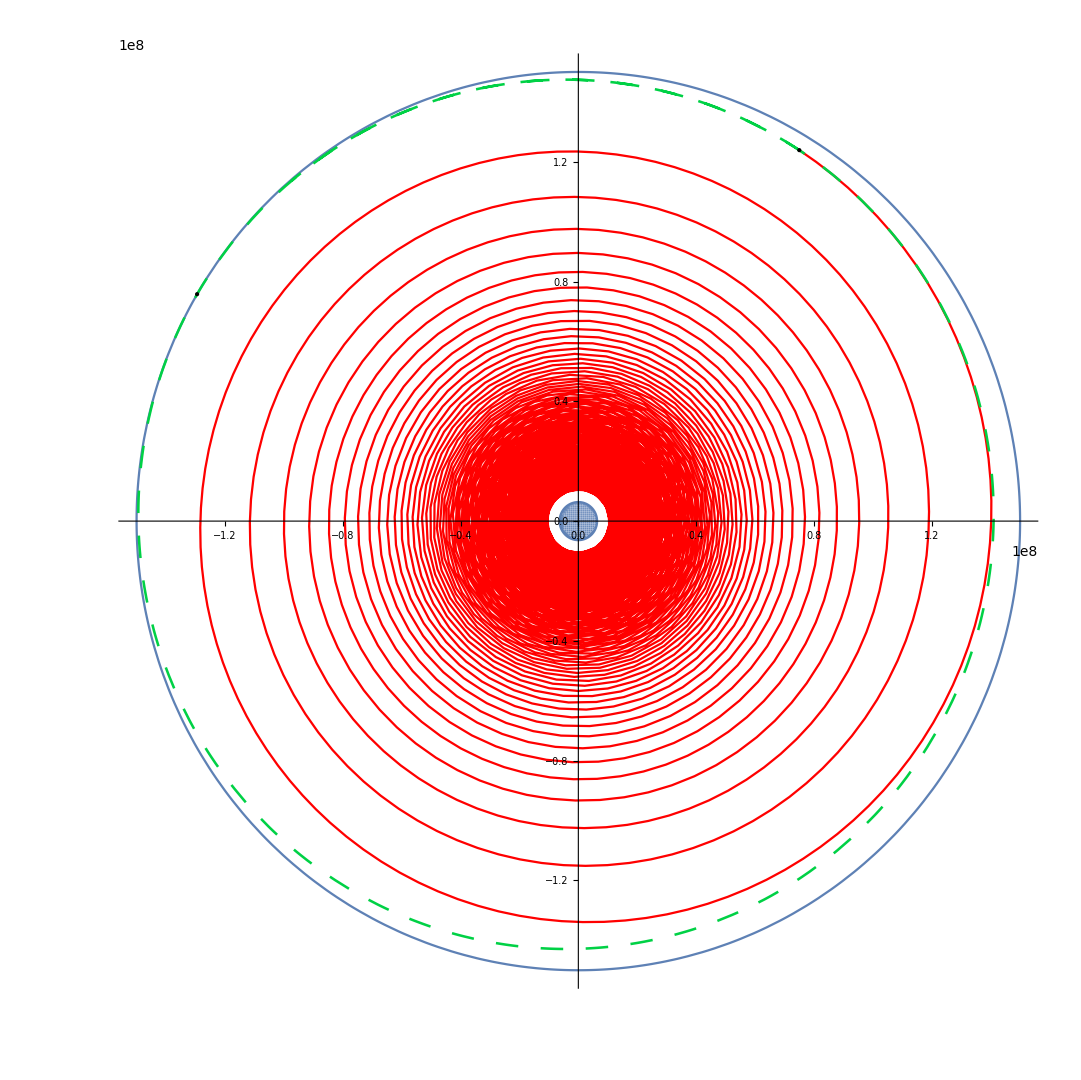

```mathematica
Show[graph1,graph2,graph3,graph4,graph5,graph6, PlotRange -> All]
```

```mathematica
ωRa=v3/Ra
```

0.0000108676

```mathematica
TRa=2Pi/ωRa
```

578160.

```mathematica
TRa/3600/24
```

6.69166

```mathematica
r1=Solution[[1,2,2]]
```

InterpolatingFunction[…][t]

```mathematica
Tact+TRa/4
```

1.23445×10^7

```mathematica
RaReal=FindMaximum[r1&& Tact<=t<=Tact+TRa,{t, Tact+TRa/4}][[1]]
```

InterpolatingFunction::dmval: Input value {1.84296×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.84296×10^7}.

1.5×10^8

```mathematica
tManevr=FindMaximum[r1&& Tact<=t<=Tact+TRa,{t, Tact+TRa/4}][[2,1,2]]
```

InterpolatingFunction::dmval: Input value {1.84296×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.84296×10^7}.

1.22864×10^7

```mathematica
r1/.t->tManevr
```

1.5×10^8

```mathematica
RpReal=FindMinimum[r1&& Tact<=t<=Tact+TRa,{t, Tact+3*TRa/4}][[1]]
```

FindMinimum::nrnum: The function value False is not a real number at {t} = {6.28774×10^6}.

1.40491×10^8

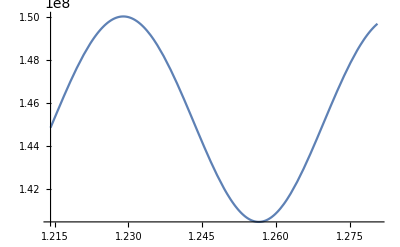

```mathematica
Plot[r1,{t,Tact,Tk+TRa}]
```

```mathematica
φ1=Solution[[1,1,2]]
```

InterpolatingFunction[…][t]

```mathematica
φ1/.t->Tk
```

1711.01

```mathematica
φ1 /(2Pi)/.t->Tk
```

272.316

## Параметры получившейся орбиты после активного участка полёта

```mathematica
eReal=(RaReal-RpReal)/(RaReal+RpReal)
pReal=RpReal*(1+eReal)
vpReal=√(μ1/pReal)*(1+eReal);
vaReal=√(μ1/pReal)*(1-eReal)
ΔvFin=v3-vaReal(*Характерестическая скорость, требуемая для выхода на круговую орбиту*)
```

0.0327323

1.4509×10^8

1603.24

26.8986

```mathematica
mfFin=.
```

```mathematica
mfFin=Solve[ΔvFin==Jid500*Log[(m1+mzevs-Δm*Tact)/(m1+mzevs-Δm*Tact-mFin)],mFin][[1,1,2]](*масса рабочего тела для последнего манёвра*)
```

14.6794

```mathematica
ΔtFin=mfFin/Δm
```

85630.

```mathematica
ΔtFin/TRa
```

0.148108

## Программа для нахождения времени активного участка полёта

```mathematica
step=10^5;
RightBorder=Tk;
LeftBorder=Tk-step;
TactIter=(LeftBorder+RightBorder)/2;
mIter[t_]:=Piecewise[{{m1+mzevs-Δm*t,t<TactIter},{m1+mzevs-Δm*TactIter,t>=TactIter}}];
SolutionIter=NDSolve[{r''[t]-r[t]*(φ'[t])^2==-μ1/(r[t])^2 , 2*r'[t]*φ'[t]+r[t]*φ''[t]==(F/mIter[t])*Piecewise[{{HeavisideTheta[TactIter-t], t!=TactIter}, {0, t==TactIter}}] ,
 φ[0]==0,φ'[0]==ωbo, r[0]==(r3+hbo),r'[0]==0},{φ[t],r[t]},{t,0,Tk+TRa}]
```

{{φ[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

```mathematica
rIter=SolutionIter[[1,2,2]];
φIter=SolutionIter[[1,1,2]];
```

```mathematica
RaIter=FindMaximum[rIter&& TactIter<=t<=TactIter+TRa,{t, TactIter+TRa/4}][[1]]
```

InterpolatingFunction::dmval: Input value {1.84839×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.84839×10^7}.

1.5221×10^8

```mathematica
RpIter=FindMinimum[rIter&& TactIter<=t<=TactIter+TRa,{t, TactIter+3*TRa/4}][[1]]
```

FindMinimum::nrnum: The function value False is not a real number at {t} = {7.35851×10^6}.

1.42271×10^8

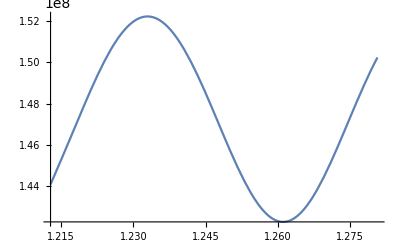

```mathematica
Plot[rIter,{t,LeftBorder,Tk+TRa}]
```

```mathematica
While[Not[Ra*(1-0.00001)<RaIter<Ra*(1+0.00001)],
If[RaIter>Ra, RightBorder=TactIter,
LeftBorder=TactIter
];
TactIter=(LeftBorder+RightBorder)/2;
SolutionIter=NDSolve[{r''[t]-r[t]*(φ'[t])^2==-μ1/(r[t])^2 , 2*r'[t]*φ'[t]+r[t]*φ''[t]==(F/mIter[t])*Piecewise[{{HeavisideTheta[TactIter-t], t!=TactIter}, {0, t==TactIter}}] ,
 φ[0]==0,φ'[0]==ωbo, r[0]==(r3+hbo),r'[0]==0},{φ[t],r[t]},{t,0,Tk+TRa}];
rIter=SolutionIter[[1,2,2]];
φIter=SolutionIter[[1,1,2]];
RaIter=FindMaximum[rIter&& TactIter<=t<=TactIter+TRa,{t, TactIter+TRa/4}][[1]];
RpIter=FindMinimum[rIter&& TactIter<=t<=TactIter+TRa,{t, TactIter+3*TRa/4}][[1]]
]
```

InterpolatingFunction::dmval: Input value {1.84464×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.84464×10^7}.

FindMinimum::nrnum: The function value False is not a real number at {t} = {6.29333×10^6}.

InterpolatingFunction::dmval: Input value {1.84276×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.84276×10^7}.

FindMinimum::nrnum: The function value False is not a real number at {t} = {6.28708×10^6}.

InterpolatingFunction::dmval: Input value {1.8437×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.8437×10^7}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMinimum::nrnum: The function value False is not a real number at {t} = {6.29021×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

```mathematica
TactIter
```

1.21419×10^7

```mathematica
RaIter
```

1.5×10^8

## Расчёт траекторий с “округлением” конечной орбиты

```mathematica
mWM[t_]:=Piecewise[{
{m1+mzevs-Δm*t,t<Tact},
{m1+mzevs-Δm*Tact,Tact<=t<(tManevr-ΔtFin/2)},{m1+mzevs-Δm*Tact-Δm*(t-(tManevr-ΔtFin/2)),(tManevr-ΔtFin/2)<=t<(tManevr+ΔtFin/2)},{m1+mzevs-Δm*Tact-mfFin,t>=(tManevr+ΔtFin/2)}
}](*Закон изменения массы*)
(*,{1,tManevr-ΔtFin/2<=t<tManevr+ΔtFin/2},{0,t>=tManevr+ΔtFin/2}*)
```

```mathematica
mWM[1.2329218768892493*^7-10^-10]
```

38193.9

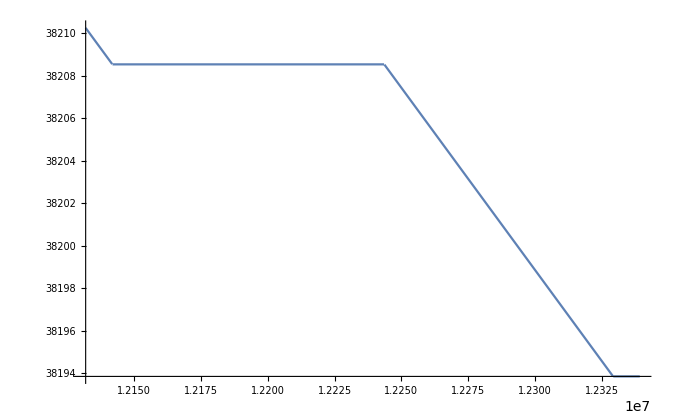

```mathematica
Plot[mWM[t],{t,Tact-10000,tManevr+ΔtFin/2+10000}]
```

```mathematica
SolutionWManevr=NDSolve[{r''[t]-r[t]*(φ'[t])^2==-μ1/(r[t])^2 , 2*r'[t]*φ'[t]+r[t]*φ''[t]==(F/m[t])*Piecewise[{{1,(t<Tact||tManevr-ΔtFin/2<=t<tManevr+ΔtFin/2)},{0,(Tact<=t<tManevr-ΔtFin/2)||(t>=tManevr+ΔtFin/2)}}],
 φ[0]==0,φ'[0]==ωbo, r[0]==(r3+hbo),r'[0]==0},{φ[t],r[t]},{t,0,Tk+2TRa}]
```

{{φ[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

```mathematica
rFin=SolutionWManevr[[1,2,2]];
φFin=SolutionWManevr[[1,1,2]];
```

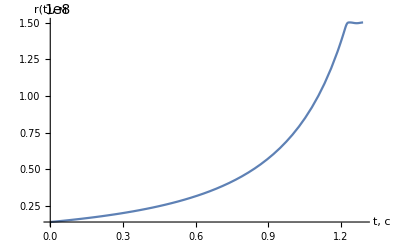

```mathematica
Plot[rFin,{t,0,tManevr+ΔtFin/2+TRa},LabelStyle->Directive[Black,Bold,Medium],AxesLabel->{"t, с","r(t), м"}]
```

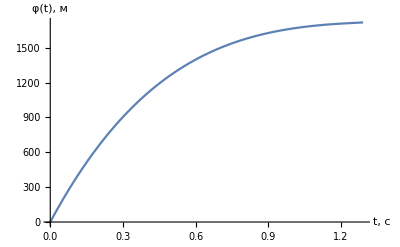

```mathematica
Plot[φFin,{t,0,tManevr+ΔtFin/2+TRa},LabelStyle->Directive[Black,Bold,Medium],AxesLabel->{"t, с","φ(t), м"}]
```

```mathematica
ActTrajectory1=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.SolutionWManevr],{t,0,Tact}, PlotStyle->{Red,Thickness[0.001]} ];
```

```mathematica
PassTrajectory1=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.SolutionWManevr],{t,Tact,tManevr-ΔtFin/2}, PlotStyle->{RGBColor[0.,0.82,0.27],Dashing[0.015, 0.015],Thickness[0.0017]},PlotLegends->Automatic];
ManevrTrajectory=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.SolutionWManevr],{t,tManevr-ΔtFin/2,tManevr+ΔtFin/2}, PlotStyle->{Red,Thickness[0.0017]} ];
PassTrajectory2=ParametricPlot[Evaluate[{r[t]*Cos[φ[t]],r[t]*Sin[φ[t]]}/.SolutionWManevr],{t,tManevr+ΔtFin/2,tManevr+ΔtFin/2+TRa}, PlotStyle->{RGBColor[0.,0.82,0.27],Dashing[0.015, 0.015],Thickness[0.0019]},PlotLegends->Automatic];
PointOff=Graphics[Point[{rFin*Cos[φFin],rFin*Sin[φFin]}]]/.t->Tact;
```

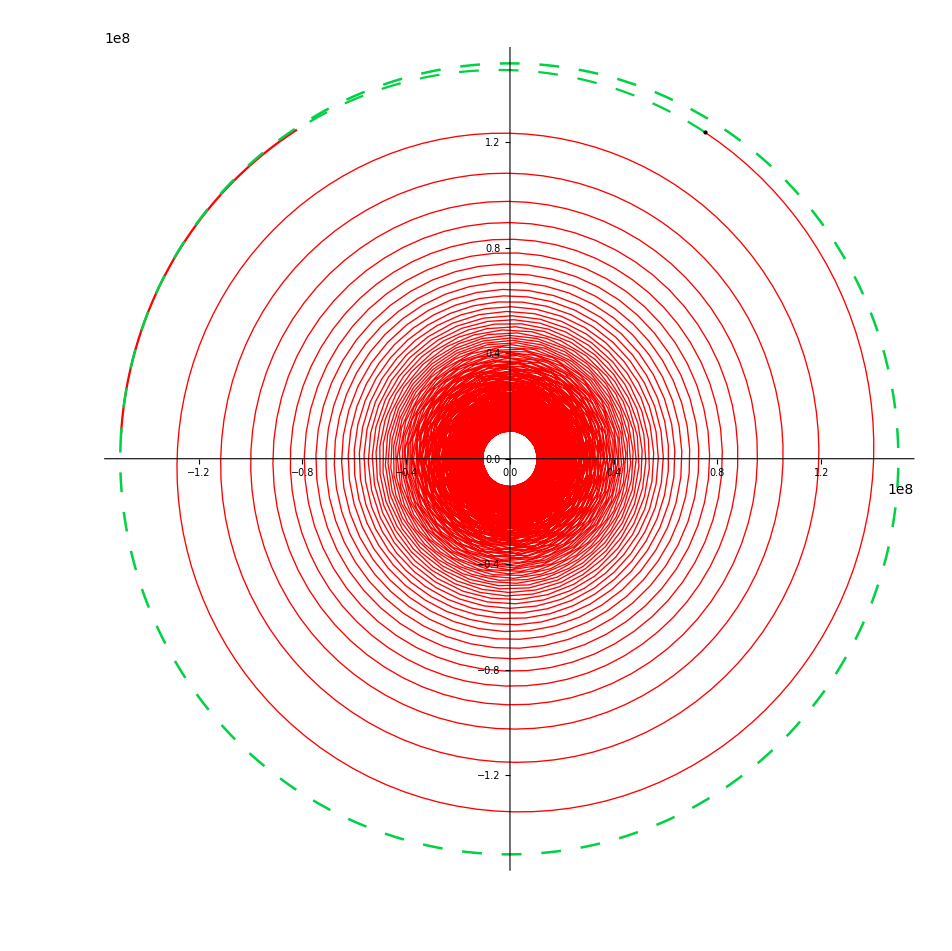

```mathematica
Show[ActTrajectory1,ManevrTrajectory,PassTrajectory1,PassTrajectory2,PointOff, PlotRange -> All]
```

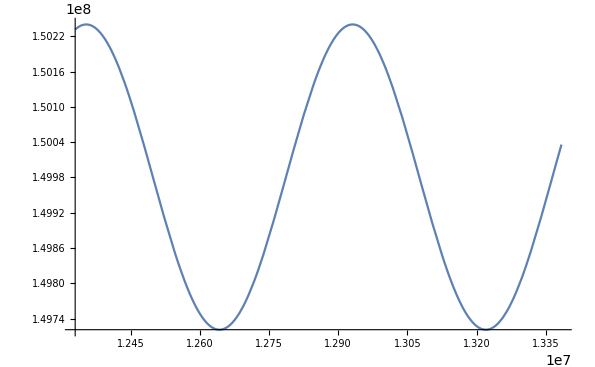

```mathematica
Plot[rFin,{t,tManevr+ΔtFin/2,Tk+ 2TRa}]
```

```mathematica
tManevr+ΔtFin/2
```

1.23292×10^7

```mathematica
2TRa
```

1.15632×10^6

```mathematica
RpFin=FindMinimum[rFin&&tManevr+ΔtFin/2<=t<=tManevr+ΔtFin/2+TRa,{t,tManevr+ΔtFin/2+TRa/2}][[1]]
```

InterpolatingFunction::dmval: Input value {1.72083×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMinimum::nrnum: The function value False is not a real number at {t} = {1.72083×10^7}.

1.4973×10^8

```mathematica
RaFin=FindMaximum[rFin&&tManevr+ΔtFin/2+TRa/2<=t<=tManevr+ΔtFin/2+3TRa/2,{t,tManevr+ΔtFin/2+TRa}][[1]]
```

InterpolatingFunction::dmval: Input value {1.75606×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {1.75606×10^7}.

1.50231×10^8

```mathematica
tManevr+ΔtFin/2+TRa/2
```

1.26183×10^7

## Параметры финальной орбиты

```mathematica
eFin=(RaFin-RpFin)/(RaFin+RpFin)
```

```mathematica
0.00167163
```

## Вековые уходы наклонения орбиты i и эксцентриситета e

```mathematica
ivosto=(51.88)*Pi/180;
ω=π/4;
Rekv=6378*10^3;
ξm= 0.56*10^(-7)*(Ra/(2*Rekv))^3;
ξs=0.26*10^(-7)*(Ra/(2*Rekv))^4;
Ts=365.256*24*3600;(*Период "оборота" Солнца вокруг Земли в секундах*)
Tm=27.322*24*3600; (*Период оборота Луны вокруг Земли в секундах*)
```

```mathematica
δi=-15/8*π/(√(1-eFin^2))*(ξs+ξm)*eFin^2*Sin[2*ivosto]*Sin[2*ω]/Degree//N
(*Вековой уход наклона орбиты за один оборот станции*)
δe=15/4*π*(ξs+ξm)*eFin*√(1-eFin^2)*Sin[ivosto]^2*Sin[2*ω]
(*Вековой уход эксцентриситета за один оборот станции*)
```

-5.38809×10^-7

7.16946×10^-6

```mathematica
Tworking=20*Ts;(*20 лет будет работать станция в секундах*)
δitotal=δi*Tworking/TRa/Degree//N
δetotal=δe*Tworking/TRa
```

-0.0337016

0.00782672

```mathematica
1.2329218703937775*^7/3600/24
```

142.699

```mathematica
φFin/(2Pi)/.t->1.2329218703937775*^7
```

272.49

```mathematica
Rvek=Solve[0.00782671645632294+ eFin==(Ra1-Rp1)/(Ra1+Rp1)&&Ra1+Rp1==RaFin+RpFin,{Ra1,Rp1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ra1→1.51405×10^8,Rp1→1.48556×10^8}}

```mathematica
Ra1=Rvek[[1,1,2]]
```

1.51405×10^8

```mathematica
Rp1=Rvek[[1,2,2]]
```

1.48556×10^8

```mathematica
evek=(Ra1-Rp1)/(Ra1+Rp1);
pvek=Rp1*(1+evek);
vAvek=√(μ1/pvek)*(1-evek)
evek1=(Ra1-Ra)/(Ra1+Ra);
pvek1=Ra*(1+evek1);
vAvek1=√(μ1/pvek1)*(1-evek1)

Δv1vek=vAvek1-vAvek
```

1614.83

1618.76

3.93752

```mathematica
Δvturn=Sqrt[2*v3^2*(1-Cos[-0.033701619126163686*Degree])]
```

0.958852

```mathematica
Solve[0.9588515671870977+3.93751655534993==3000*Log[(40000+mpodd)/40000],mpodd]
```

{{mpodd→65.3382}}

```mathematica
Solve[0.9588515671870977+3.93751655534993==3000*Log[(40000+mpodd)/40000],mpodd]
```

{{mpodd→65.3382}}

```mathematica
Δm*Tact+mfFin
```

2096.14